Si può automatizzare la ricerca della biforcazione. Per determinare la biforcazione n-esima, si parte da un appropriato valore di μ inferiore a quello di biforcazione (stimato ad occhio) e si confrontano, per un N opportunamente grande, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini, non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi, siamo arrivati alla biforcazione.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
dist[μ_,x0_,Ν_,n_]:=Abs[fn[μ,x0,Ν]-fn[μ,x0,Ν+2^n]]
indagine[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,Ν,n]},{μ,min,max,step}]
sospetto[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

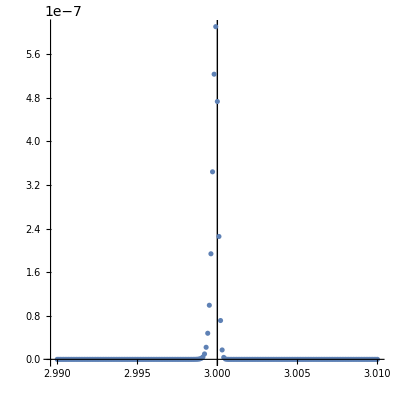

```mathematica
ListPlot[indagine[2,0.4,10^4,{2.99,3.01,10^-4}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{3,0},{3,1}}]}]
```

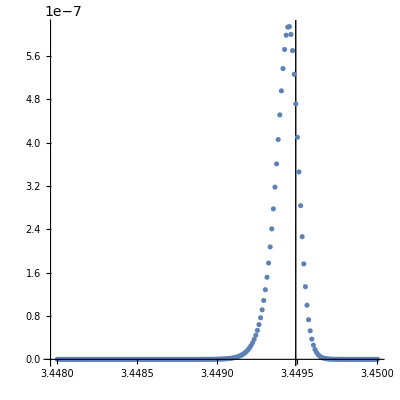

```mathematica
ListPlot[indagine[3,0.4,10^4,{3.448,3.45,10^-5}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{1+√6,0},{1+√6,1}}]}]
```

```mathematica
(1+√6-3.4494459999999996)/(1+√6)
```

0.0000126809

Quindi non solo il metodo pare funzionare, ma gli errori numerici che compie potrebbero essere inferiori all’1%! Godo.

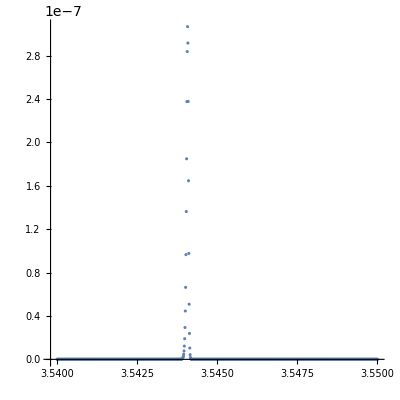

```mathematica
ListPlot[indagine[4,0.4,10^4,{3.54,3.55,10^-5}],AspectRatio->1,PlotRange->Full]
```

```mathematica
sospetto[4,0.4,10^4,{3.54,3.55,10^-5}]
```

{{3.54407,3.06786×10^-7}}

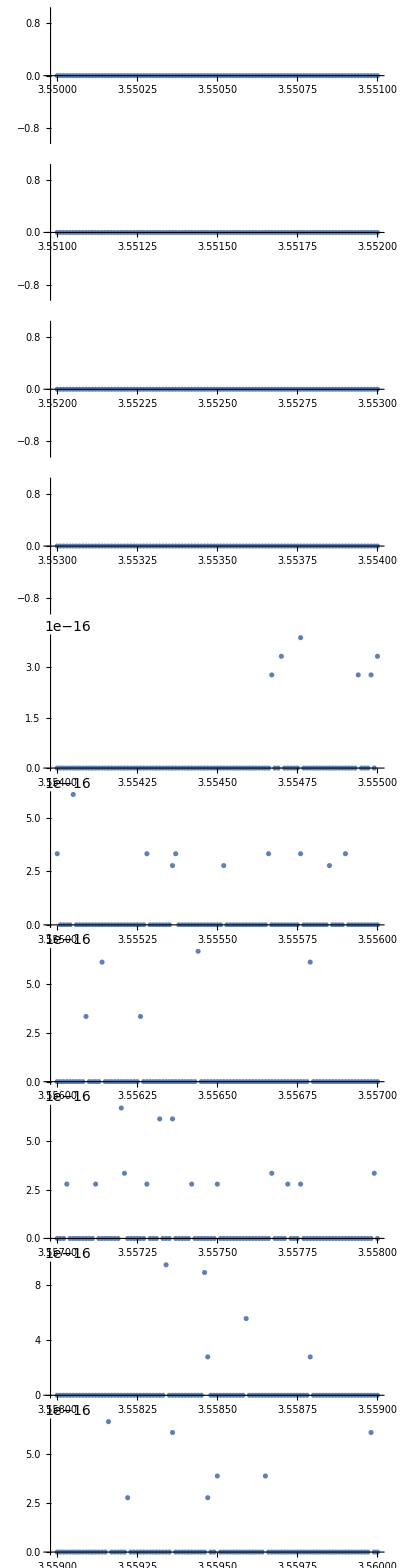

```mathematica
Column[Table[ListPlot[indagine[5,0.4,10^5,{x,x+10^-3,10^-5}],AspectRatio->1,PlotRange->Full,Ticks->{Automatic,None}],{x,3.55,3.559,10^-3}]]
```